```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
(*LS-Periodogram*)
LS[tx_, nP_] := 
 LS[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]/∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
LSCos[tx_, nP_] := 
 LSCos[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]/∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
T[periodogram_,rankmax_]:=T[periodogram,rankmax]=Block[{power,ωmax,period},power=Table[periodogram[[i,2]],{i,1,Length[periodogram]}];
ωmax=periodogram[[Position[power,RankedMax[power,rankmax]][[1,1]],1]];
{period=2 π/ωmax,RankedMax[power,rankmax]}];
p[z_,n_]:=p[z,n]=1-(1-Exp[-z])^n;
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

# Lomb Scargle

```mathematica
rundat={};
starttime=0;
pta10=pta20=fta10=fta20=erra10=erra20=fta102=fta202={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
ptarun=Table[{},{k,1,dimdesc}];ptarun2=Table[{},{k,1,dimdesc}];
ftarun=Table[{},{k,1,dimdesc}];ftarun2=Table[{},{k,1,dimdesc}];
errarun=Table[{},{k,1,dimdesc}];errarun2=Table[{},{k,1,dimdesc}];
tsadd=2*PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>20&&descdat[[i]][[5]]<9000(*&&MemberQ[{1,2,3,4,5,39,40,41},i]*))
,
(*Print[descdat[[i]][[4]]];*)
rundat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimrundat=Dimensions[rundat][[1]];
If[i==1,starttime=rundat[[1]][[1]]];
(*For-A*tf/ts*)
ptarun[[i]]=Table[
{
N[(rundat[[;;,1]][[k]]-starttime)/(86164.09054)](*Mod[(rundat[[;;,1]][[k]]-starttime)/(86164.09054),1]*),
{
((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[1]],
Abs[((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[2]]]
}
},
{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}
];
ftarun[[i]]=Transpose[{ptarun[[i]][[;;,1]],ptarun[[i]][[;;,2]][[;;,1]]}];
errarun[[i]]=Abs[ptarun[[i]][[;;,2]][[;;,2]]];
(*For-A*)
ptarun2[[i]]=Table[{N[(rundat[[;;,1]][[k]]-starttime)/(86164.09054)],{rundat[[;;,{2,3}]][[k]][[1]],Abs[rundat[[;;,{2,3}]][[k]][[2]]]}},{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}];
ftarun2[[i]]=Transpose[{ptarun2[[i]][[;;,1]],ptarun2[[i]][[;;,2]][[;;,1]]}];
errarun2[[i]]=Abs[ptarun2[[i]][[;;,2]][[;;,2]]];
(**)
If[descdat[[i]][[6]]==10,
{
bpt10=Join[bpt10,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{8,9}]]}]];
bft10=Join[bft10,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta10=Join[pta10,ptarun[[i]]];
fta10=Join[fta10,ftarun[[i]]];
erra10=Join[erra10,errarun[[i]]];
},
{
bpt20=Join[bpt20,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{8,9}]]}]];
bft20=Join[bft20,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta20=Join[pta20,ptarun[[i]]];
fta20=Join[fta20,ftarun[[i]]];
erra20=Join[erra20,errarun[[i]]];
}
];
bpt0=Join[bpt0,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{6,7}]]}]];
bft0=Join[bft0,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];
];
lvl3={{}};
(*Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3sidereal.dat"],lvl3];*)
];
(**)
cutoff=3;
cleanpta10=Select[pta10,Abs[#[[2]][[1]]]<cutoff&];
cleanpta20=Select[pta20,Abs[#[[2]][[1]]]<cutoff*1.5&];
cleanfta10=Table[{cleanpta10[[k]][[1]],cleanpta10[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta10][[1]]}];
cleanerra10=Table[cleanpta10[[k]][[2]][[2]],{k,1,Dimensions[cleanpta10][[1]]}];
cleanfta20=Table[{cleanpta20[[k]][[1]],cleanpta20[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta20][[1]]}];
cleanerra20=Table[cleanpta20[[k]][[2]][[2]],{k,1,Dimensions[cleanpta20][[1]]}];
(**)
mcruns=25;
np=2000;
gramftamc=Table[{},{k,1,mcruns}];
gramftamc2=Table[{},{k,1,mcruns}];
totdat=Join[cleanpta10,cleanpta20];
totdatft=Join[cleanfta10,cleanfta20];
```

## MC+LS

```mathematica
Parallelize[
For[j=1,j≤mcruns,j++,
cleanftamc={};
For[i=1,i≤Dimensions[totdat][[1]],i++,
RandomSeed[CurrentDate[]];
cleanftamc=AppendTo[cleanftamc,{totdat[[i]][[1]],RandomVariate[NormalDistribution[totdat[[i]][[2]][[1]],totdat[[i]][[2]][[2]]]]}];
];
gramftamc[[j]]=LS[cleanftamc,np];
gramftamc2[[j]]=LSCos[cleanftamc,np];
];
gramfta=LS[totdatft,np];
gramfta2=LSCos[totdatft,np];
gramftamcm=Mean[gramftamc];
gramftamcm2=Mean[gramftamc2];
gramftamcs=StandardDeviation[gramftamc];
gramftamcs2=StandardDeviation[gramftamc2];
]//AbsoluteTiming
```

{2509.78,Null}

```mathematica
(*Dump Old data set*)
```

```mathematica
Export[StringJoin[descDir,seperator,"LS-Sin-data.dat"],gramfta]
Export[StringJoin[descDir,seperator,"LS-Cos-data.dat"],gramfta2]
Export[StringJoin[descDir,seperator,"LS-Sin-mc_mean.dat"],gramftamcm]
Export[StringJoin[descDir,seperator,"LS-Cos-mc_mean.dat"],gramftamcm2]
Export[StringJoin[descDir,seperator,"LS-Sin-mc_sigma.dat"],gramftamcs]
Export[StringJoin[descDir,seperator,"LS-Cos-mc_sigma.dat"],gramftamcs2]
```

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Sin-data.dat

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Cos-data.dat

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Sin-mc_mean.dat

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Cos-mc_mean.dat

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Sin-mc_sigma.dat

C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online\LS-Cos-mc_sigma.dat

```mathematica
(*DO NOT RUN Usually, Loading old data set*)
```

```mathematica
gramfta=Import[StringJoin[descDir,seperator,"LS-Sin-data.dat"]];
gramfta2=Import[StringJoin[descDir,seperator,"LS-Cos-data.dat"]];
gramftamcm=Import[StringJoin[descDir,seperator,"LS-Sin-mc_mean.dat"]];
gramftamcm2=Import[StringJoin[descDir,seperator,"LS-Cos-mc_mean.dat"]];
gramftamcs=Import[StringJoin[descDir,seperator,"LS-Sin-mc_sigma.dat"]];
gramftamcs2=Import[StringJoin[descDir,seperator,"LS-Cos-mc_sigma.dat"]];
np=2000;
mcruns=25;
```

```mathematica
(*DO NOT RUN Usually, Loading old data set*)
```

```mathematica
gramfta=Import[StringJoin[descDir,seperator,"LS-Sin-data2.dat"]];
gramfta2=Import[StringJoin[descDir,seperator,"LS-Cos-data2.dat"]];
gramftamcm=Import[StringJoin[descDir,seperator,"LS-Sin-mc_mean2.dat"]];
gramftamcm2=Import[StringJoin[descDir,seperator,"LS-Cos-mc_mean2.dat"]];
gramftamcs=Import[StringJoin[descDir,seperator,"LS-Sin-mc_sigma2.dat"]];
gramftamcs2=Import[StringJoin[descDir,seperator,"LS-Cos-mc_sigma2.dat"]];
np=160000;
mcruns=25;
```

## Plotting

```mathematica
lineStyle={Thick,Black};
ln1=Line[{{ 2Pi,0},{2 Pi,3}}];
ln2=Line[{{ 4Pi,0},{4 Pi,3}}];
ptgramfta=Transpose[{gramfta[[;;,1]],Sqrt[gramfta[[;;,2]]/(4Pi)]}];
ptgramftamcm=Transpose[{gramftamcm[[;;,1]],Sqrt[gramftamcm[[;;,2]]/(4Pi)]}];
ptgramftamcm1=Transpose[{gramfta[[;;,1]],Sqrt[1.39^2]*Sqrt[(gramftamcm[[;;,2]]+gramftamcs[[;;,2]])/(4Pi)]}];
ptgramftamcm95=Transpose[{gramfta[[;;,1]],Sqrt[1.96^2]*Sqrt[(gramftamcm[[;;,2]]+gramftamcs[[;;,2]])/(4Pi)]}];
ptgramfta2=Transpose[{gramfta2[[;;,1]],Sqrt[gramfta2[[;;,2]]/(2Pi)]}];
ptgramftamcm2=Transpose[{gramftamcm2[[;;,1]],Sqrt[gramftamcm2[[;;,2]]/(2Pi)]}];
ptgramftamcm12=Transpose[{gramfta2[[;;,1]],Sqrt[1.39^2]*Sqrt[(gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]])/(4Pi)]}];
ptgramftamcm952=Transpose[{gramfta2[[;;,1]],Sqrt[1.96^2]*Sqrt[(gramftamcm2[[;;,2]]+ gramftamcs2[[;;,2]])/(4Pi)]}];
ptgramftap=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramfta[[;;,2]]/gramfta2[[;;,2]]]]}];
ptgramftamcmp=Transpose[{gramftamcm2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]/gramftamcm2[[;;,2]]]]}];
ptgramftamcm1p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]]]]}];
ptgramftamcm95p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+1.96 gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+1.96 gramftamcs2[[;;,2]]]]}];
val2pi=Nearest[ptgramfta[[;;,1]],2Pi][[1]];
Print["Amplitude @ 2π: ", amp2pi=ptgramfta[[Position[ptgramfta,val2pi][[1]][[1]]]][[2]]];
Print["Amplitude @ 2π: ", pow2pi=amp2pi^2];
val4pi=Nearest[ptgramfta[[;;,1]],4Pi][[1]];
Print["Amplitude @ 4π: ", amp4pi=ptgramfta[[Position[ptgramfta,val4pi][[1]][[1]]]][[2]]];
Print["Amplitude @ 4π: ", pow4pi=amp4pi^2];
Export[StringJoin[PicDir,seperator,"Sidereal_pow-1.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{6.11,6.44},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_pow-2.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{2*{6.11,6.44},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_pow_all.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.002],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{0.001,49.999},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
(*ListPlot[{ptgramfta2,ptgramftamcm2,ptgramftamcm12,ptgramftamcm952},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{5.9,6.7},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]
ListPlot[{Sqrt[ptgramfta^2+ptgramfta2^2]/Sqrt[2],Sqrt[ptgramftamcm^2+ptgramftamcm2^2]/Sqrt[2],Sqrt[ptgramftamcm1^2+ptgramftamcm12^2]/Sqrt[2],Sqrt[ptgramftamcm95^2+ptgramftamcm952^2]/Sqrt[2]},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{6.1,6.45},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]*)
Export[StringJoin[PicDir,seperator,"Sidereal_phase_1.png"],ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{{6.11,6.44},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_phase_2.png"],ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{2*{6.11,6.44},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
```

Amplitude @ 2π: 0.123493

Amplitude @ 2π: 0.0152504

Amplitude @ 4π: 0.220211

Amplitude @ 4π: 0.0484927

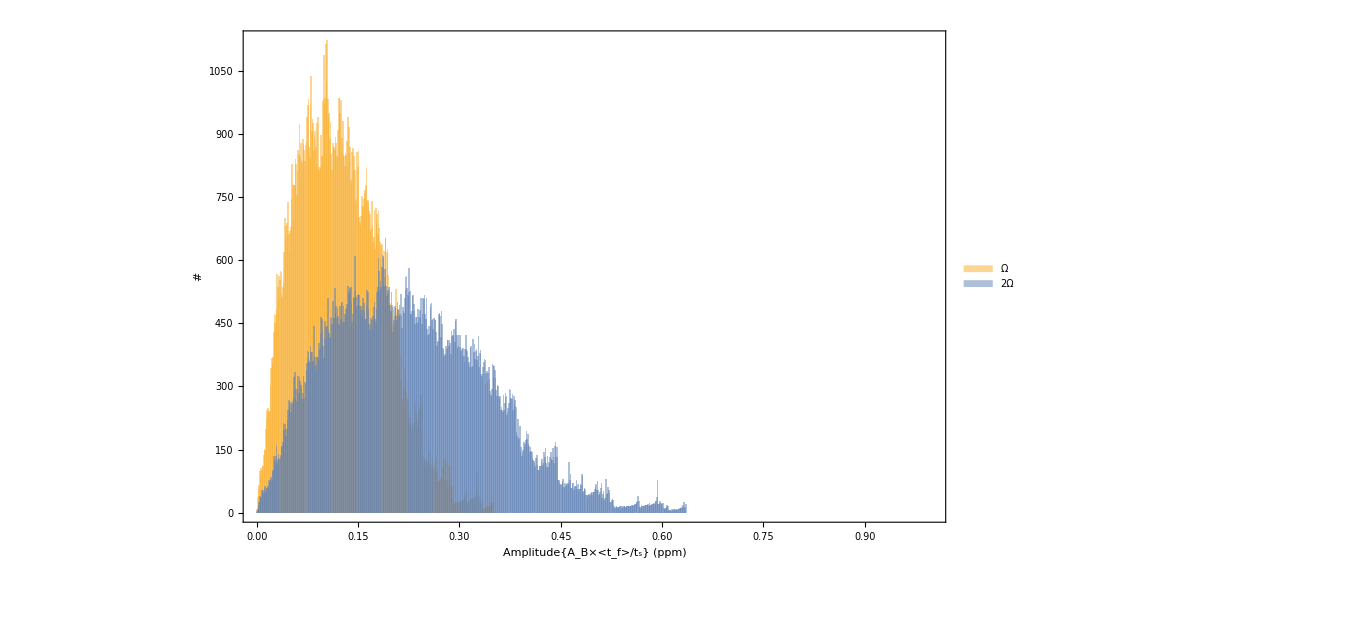
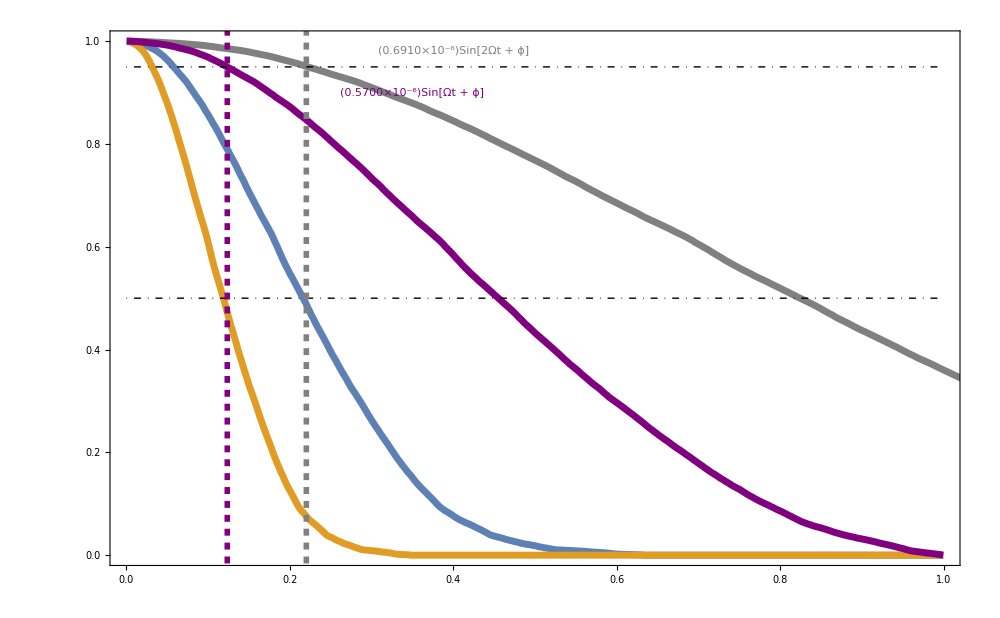

```mathematica
histgramfta=HistogramList[ptgramfta[[;;,2]]/1.1,{0,1,.001}];
tothistgramfta=Total[histgramfta[[2]]];
pthistgramfta=Table[{histgramfta[[1]][[k]]+(histgramfta[[1]][[2]]-histgramfta[[1]][[1]])/2,1-Total[histgramfta[[2]][[;;k]]]/tothistgramfta},{k,1,Dimensions[histgramfta[[2]]][[1]]}];
histgramfta2=HistogramList[ptgramfta[[;;,2]]/2,{0,1,.001}];
tothistgramfta2=Total[histgramfta2[[2]]];
pthistgramfta2=Table[{histgramfta2[[1]][[k]]+(histgramfta2[[1]][[2]]-histgramfta2[[1]][[1]])/2,1-Total[histgramfta2[[2]][[;;k]]]/tothistgramfta2},{k,1,Dimensions[histgramfta2[[2]]][[1]]}];
(***)
histgramfta3=HistogramList[ptgramfta[[;;,2]]*.22*1.96/amp2pi,{0,2,.001}];
tothistgramfta3=Total[histgramfta3[[2]]];
pthistgramfta3=Table[{histgramfta3[[1]][[k]]+(histgramfta3[[1]][[2]]-histgramfta3[[1]][[1]])/2,1-Total[histgramfta3[[2]][[;;k]]]/tothistgramfta3},{k,1,Dimensions[histgramfta3[[2]]][[1]]}];
(**)
histgramfta4=HistogramList[ptgramfta[[;;,2]]*.22*1.96/amp4pi,{0,1,.001}];
tothistgramfta4=Total[histgramfta4[[2]]];
pthistgramfta4=Table[{histgramfta4[[1]][[k]]+(histgramfta4[[1]][[2]]-histgramfta4[[1]][[1]])/2,1-Total[histgramfta4[[2]][[;;k]]]/tothistgramfta4},{k,1,Dimensions[histgramfta4[[2]]][[1]]}];
(***)
lineStyle1={Thick,Dashed,Black};
lineStyle2={Thickness[.004],Dashed,Purple};
lineStyle3={Thickness[.004],Dashed,Gray};
ln11=Line[{{ amp2pi,-10},{amp2pi,100}}];
ln21=Line[{{amp4pi,-10},{amp4pi,100}}];
Overlay[{
Histogram[{ptgramfta[[;;,2]]/2,ptgramfta[[;;,2]]/1.1},{0,1,.001},ChartLegends->{"Ω","2Ω"},ImagePadding->100,Frame->{True,True,False,False},FrameLabel->{"Amplitude{A_B×<t_f>/t_s} (ppm)","#"},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{{Thickness[.004],Red},{Thickness[.004],Red},Automatic,Automatic}],
Show[{
ListLinePlot[{pthistgramfta,pthistgramfta2,pthistgramfta3,pthistgramfta4},PlotRange->{{0,1},Automatic},ImagePadding->100,Frame->{False,False,True,True},PlotStyle->{{Thickness[.005],Automatic},{Thickness[.005],Automatic},{Thickness[.005],Gray},{Thickness[.005],Purple}},FrameLabel->{{"",Rotate["p-value",180 Degree]},{"",""}},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{Automatic,Automatic,{Thickness[.004],Blue},{Thickness[.004],Blue}},
Epilog->{
{Directive[lineStyle2],ln11,Text[Style["(0.5700×10^-6)Sin[Ωt + ϕ]",FontSize->Large],{.35,.90}]},
{Directive[lineStyle3],ln21,Text[Style["(0.6910×10^-6)Sin[2Ωt + ϕ]",FontSize->Large],{.4,.98}]}
}],
Plot[{.5,.95(*,p[(z*50)^2,np],p[z*33,np]*)},{z,0,1},ImagePadding->100,Frame->{False,False,False,False},PlotStyle->{{DotDashed, Thin,Black},{DotDashed, Thin,Black},{Thickness[.005],Purple},{Thickness[.005],Gray},},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{None,None,{Thickness[.004],Blue},{Thickness[.004],Blue}}]
}]
}]
```

# Test-data-Amplitude-exclusion

```mathematica
AbsoluteTiming[
nsamplep=2000;
sampledat2pi[aa_]:=Table[{totdatft[[k]][[1]],aa Sin[2Pi totdatft[[k]][[1]]]},{k,1,Dimensions[totdatft][[1]]}];
gramsamplefta=LS[sampledat2pi[.03],nsamplep];
ptgramsamplefta=Transpose[{gramsamplefta[[;;,1]],Sqrt[gramsamplefta[[;;,2]]/(4Pi)]}];
histgramsamplefta=HistogramList[ptgramsamplefta[[;;,2]],{0,1,.001}];
tothistgramsamplefta=Total[histgramsamplefta[[2]]];
pthistgramsamplefta4=Table[{histgramsamplefta[[1]][[k]]+(histgramsamplefta[[1]][[2]]-histgramsamplefta[[1]][[1]])/2,1-Total[histgramsamplefta[[2]][[;;k]]]/tothistgramsamplefta},{k,1,Dimensions[histgramsamplefta[[2]]][[1]]}];
]
```

$Aborted

```mathematica
ListLinePlot[{pthistgramsamplefta,pthistgramsamplefta2,pthistgramsamplefta3,pthistgramsamplefta4},ImagePadding->90,Frame->{False,False,True,True},PlotStyle->Thickness[.005],FrameLabel->{{"",Rotate["p-value",180 Degree]},{"",""}},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{Automatic,Automatic,{Thickness[.004],Blue},{Thickness[.004],Blue}},Epilog->{Directive[lineStyle1],ln11,ln21}]
(*
Overlay[{
Histogram[{ptgramsamplefta[[;;,2]]},{0,1,.001},ImagePadding->90,Frame->{True,True,False,False},ChartStyle->{Pink,Gray},FrameLabel->{"Amplitude{A_B×<t_f>/t_s} (ppm)","#"},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{{Thickness[.004],Red},{Thickness[.004],Red},Automatic,Automatic}],
ListLinePlot[{pthistgramsamplefta,pthistgramsamplefta2},ImagePadding->90,Frame->{False,False,True,True},PlotStyle->Thickness[.005],FrameLabel->{{"",Rotate["p-value",180 Degree]},{"",""}},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{Automatic,Automatic,{Thickness[.004],Blue},{Thickness[.004],Blue}},Epilog->{Directive[lineStyle1],ln11,ln21}]
}]
*)
```

```mathematica
Export[StringJoin[descDir,seperator,"all_lvl3sidereal.dat"],regreport["ParameterTable"][[1]][[1]][[2;;]]]
```

χ^2 {10,20}μT : { 5.35697 , 14.2098 }

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.104546 | 0.202801 | 0.515509 | 0.607395
b1 | -0.179417 | 0.170303 | -1.05352 | 0.294777
b2 | 0.0945746 | 0.295763 | 0.319765 | 0.749849
phi | 0.085153 | 0.324928 | 0.262067 | 0.793837

{0.104546,-0.179417,0.0945746,0.085153}

{0.202801,0.170303,0.295763,0.324928}

{0.515509,-1.05352,0.319765,0.262067}

```mathematica
totdatft
```

{{0.,0.18},{0.125995,1.3},{0.250625,0.09},{0.373862,0.47},{0.542278,0.65},{0.817415,1.03},{0.96482,-0.38},{1.09913,0.68},{1.22415,0.65},{1.45171,-1.88},{1.79571,-0.12},{1.93599,0.94},{2.06671,0.44},{2.19514,0.21},{2.32358,0.71},{2.44861,2.33},{3.27761,-0.41},{3.42556,-2.62},{3.82399,-1.5},{4.10874,-1.65},{4.25087,-0.79},{4.37611,-0.53},{4.50818,-0.26},{4.63947,1.03},{4.7702,1.18},{4.90036,-0.26},{5.0292,1.03},{5.16177,-2.5},{5.28964,0.74},{5.74771,0.44},{5.96568,-0.77},{6.32979,2.06},{6.88795,-0.85},{7.10704,0.46},{7.32844,0.68},{7.54023,-0.89},{7.84116,-1.87},{10.0521,-0.34},{10.2659,1.05},{10.4771,-0.62},{10.6923,1.16},{10.9798,-1.25},{11.2154,0.23},{11.4366,-0.64},{11.6554,1.21},{11.8721,0.12},{12.0901,0.82},{18.1524,1.42},{18.2186,-2.68},{18.4091,-2.36},{18.4922,0.18},{18.57,-2.36},{18.688,0.2},{18.7793,2.42},{18.862,0.39},{18.9493,-0.94},{19.0102,-0.3},{19.0794,0.73},{19.1486,-2.13},{19.2759,0.},{19.5407,-1.2},{19.8261,-1.43},{19.893,0.56},{19.9599,1.26},{20.0827,-1.78},{20.1675,1.3},{20.2444,1.74},{20.3612,-0.2},{20.452,-0.09},{20.5327,-2.8},{31.1836,-0.81},{31.4101,1.74},{31.6241,0.04},{31.8634,-0.22},{32.1433,0.53},{32.3604,-0.42},{32.572,-0.66},{32.7842,1.1},{33.002,0.95},{33.2186,-1.54},{38.5625,1.5},{38.7365,-0.93},{38.9341,-0.27},{39.4131,2.8},{39.5484,1.65},{39.679,-1.99},{39.8048,3.88},{40.0558,-2.41},{40.1839,-3.01},{40.3181,0.51},{40.4524,0.72},{40.5852,-0.21},{40.7166,1.41},{40.8415,-3.79},{40.9766,2.29},{41.1088,-1.38},{41.2421,1.23},{41.3671,-0.24},{41.4939,0.9}}

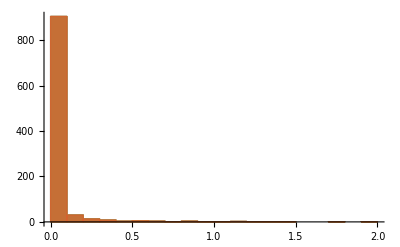
{3473.29,-Graphics-}

```mathematica
AbsoluteTiming[Histogram[Table[LS[Table[{k,l Sin[2Pi k]},{k,1,40,.1}],1000][[;;,2]],{l,.1,10.1,1}],{0,2,.1}]]
```